Approximate Clamped Cosine

```mathematica
G[v_,{p_,λ_,μ_}]:=μ*Exp[λ*(Dot[v,p]-1)];
GVec[{x_,y_,z_},{p_,λ_,μ_}]:=G[{x,y,z},{p,λ,μ}];
Print[">SG:"  TraditionalForm[G[v,{p,λ,μ}]]];
```

>SG: (μ ⅇ^(λ (v.p-1)))

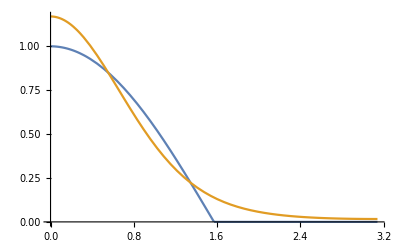

```mathematica
ClampedCos[x_]:=Max[0,Cos[x]];
(*All Frequency...Eq40*)
ApproxCC[x_]:=1.170*Exp[2.133*(Cos[x]-1)];
Plot[{ClampedCos[x],ApproxCC[x]},{x,0,π}]
```

```mathematica
FindMinimum[
	NIntegrate[Abs[ClampedCos[x]-μ*Exp[λ*(Cos[x]-1)]],{x,0,π},
	PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],
{μ,1.170},{λ,2.133}]
```

NIntegrate::inumr: The integrand Abs[-ⅇ^(λ (-1+Cos[x])) μ+Max[0,Cos[x]]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand Abs[-1. ⅇ^(λ (-1.+Cos[x])) μ+Max[0,Cos[x]]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.185145,{μ→1.06596,λ→1.98841}}

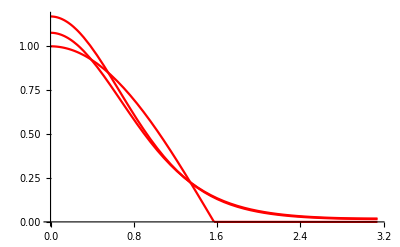

```mathematica
ApproxNew[x_]:=1.077094*Exp[2.01906*(Cos[x]-1)];
Plot[{ApproxNew[x],ClampedCos[x],ApproxCC[x]},{x,0,π},PlotStyle->{Red,Green,Blue}]
```